```mathematica
<<peeters` ;
peeters`setGitDir[ "figures\\ece1229" ]
```

Part (e).  Numerical calculations of the directivity.

```mathematica
ClearAll[af,afn,Uccube, dir, nvalues, Umax, Prad, elementFactor, t, p, dirWithEF, dirWithoutEF, dirGWithEF, dirGWithoutEF ]

(*n,theta,phi*)
af:= 2 Cos[ 2 Pi #1 Sin[#2]Cos[#3 - Pi/4] ] - 2 Cos[ 2 Pi #1 Sin[#2] Cos[#3 + Pi/4]] & ;
afn:=  af[ Sqrt[2] #1, #2, #3] & ;

(*theta, withEF=1/-1*)
elementFactor := Sin[#1]^2  UnitStep[ #2 ] + UnitStep[ -#2] & ;

(*n,theta,phi,withEF=1/-1*)
Uccube :=  elementFactor[#2,#4 ]afn[#1, #2, #3]^2 & ;
(*n,withEF=1/-1*)
Umax := 
NMaximize[{Uccube[#1, t, p, #2], 0 ≤ p ≤ Pi/2,  0 ≤ t ≤ Pi},{p, t}] &;
Prad := NIntegrate[Uccube[#1, t, p, #2]Sin[t], {p, 0, Pi/2}, {t, 0, Pi}]  &;

withEF = 1 ;
withoutEF = -1 ;
dirWithEF := 4 Pi Umax[#1, withEF][[1]]/Prad[#1, withEF] & ;
dirWithoutEF := 4 Pi Umax[#1, withoutEF][[1]]/Prad[#1, withoutEF]  & ;

(*using  Prof G. E.'s  factorization of the AF:*)
afG:=-4 Sin[2 Pi #1 Sin[#2] Sin[#3]] Sin[2 Pi #1 Sin[#2] Cos[#3]] &;
UccubeG :=  elementFactor[#2,#4 ] afG[#1, #2, #3]^2  &;
UmaxG:= 
NMaximize[{UccubeG[#1, t, p, #2], 0 ≤ p ≤ Pi/2,  0 ≤ t ≤ Pi},{p, t}] & ;
PradG := NIntegrate[UccubeG[#1, t, p, #2]Sin[t], {p, 0, Pi/2}, {t, 0, Pi}] & ;
dirGWithEF:= 4 Pi UmaxG[#1, withEF][[1]]/PradG[#1, withEF] & ;
dirGWithoutEF:= 4 Pi UmaxG[#1, withoutEF][[1]]/PradG[#1, withoutEF] & ;

nvalues = {0.01, 1/8, 1/4, 1/2} ;
{nvalues, dirWithEF[#]&/@ nvalues(*,dirGWithEF[#]&/@ nvalues*), dirWithoutEF[#]&/@ nvalues(*,dirGWithoutEF[#]&/@ nvalues*)} // Transpose // TableForm
```

0.01 | 17.4974 | 14.9972
1/8 | 17.0984 | 14.5556
1/4 | 15.8698 | 13.1705
1/2 | 14.3155 | 15.1262

For directivity approximation:

```mathematica
ClearAll[p]
Cos[p -Pi/4]^2 - Cos[p + Pi/4]^2 // TrigExpand 

Integrate[ Sin[2p]^2, {p, 0, Pi/2}]
Integrate[ Sin[t]^#, {t, 0, Pi}] & /@ {7,5,3, 1}

35/2 / (3/2) // N
```

2 Cos[p] Sin[p]

π/4

{32/35,16/15,4/3,2}

11.6667

Part (d).  Plots of |AF|^2 in XY plane.

-Graphics3D-

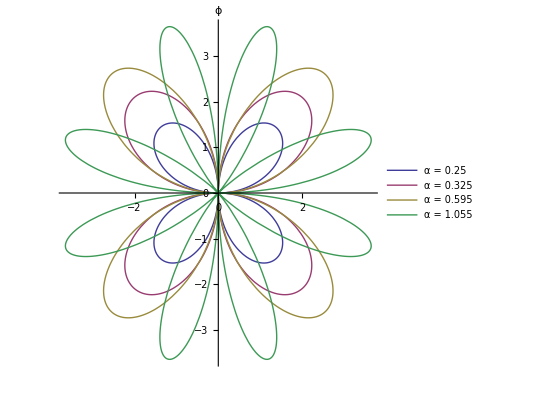

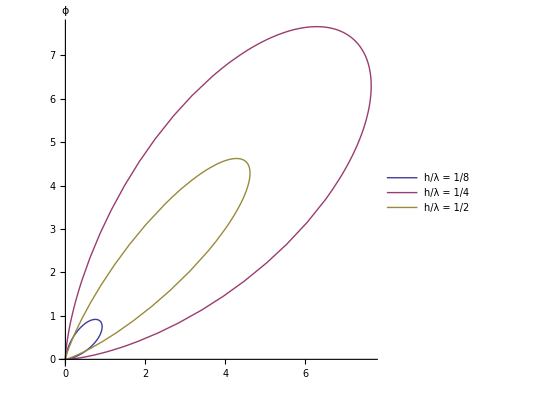

-Graphics3D-

```mathematica
ClearAll[aa, xx,  pp]

pp = Plot3D[ af[a,Pi/2, p], {a, 0, 1.5}, {p, 0, 2 Pi}, AxesLabel -> {α, ϕ}]

aa = {0.25,0.325,0.595,1.055} ;

(* aa = {0.1, 0.25, 0.5} ;*)
xx = PolarPlot[af[#, Pi/2, p] &/@ aa // Evaluate, {p, 0, 2 Pi}, AxesLabel -> ϕ, PlotLegends -> Placed[Row[{"α = ", #}]&/@aa, {Right,Bottom}]]

(*bb = Table[i/10, {i, 10}] ;
bb = aa ;*)
bb= {1/8, 1/4, 1/2} ;
yy = PolarPlot[afn[#, Pi/2, p]^2 &/@ bb // Evaluate, {p, 0, Pi/2}, AxesLabel -> ϕ, PlotLegends -> Placed[Row[{"h/λ = ", #}]&/@bb, {Right,Bottom}]]


zz = With[{a=0.6900000000000001,pg="Quality",range=18},Show[ParametricPlot3D[{af[a,t,p]^2 rcap[t,p]},{t,0,π},{p,0,π/2},AxesLabel->{x,y,z},PlotRange->{{0,range},{0,range},{-range,range}},PlotStyle->Directive[Opacity[0.6]],ViewPoint->{2.616433634989163,1.0060144996548517,1.89531260223257},PerformanceGoal->pg],axes]]
```

```mathematica
Manipulate[ PolarPlot[afn[n, Pi/2, p]^2,{p, 0, Pi/2}, AxesLabel -> ϕ ],
{{n,0.25,"h/λ"}, 0, 3, Appearance->"Labeled"}]

(*Visualize the array factor (squared),with a control for h.*)
Manipulate[ 

Show[
ParametricPlot3D[ 
{afn[n, t, p]^2 rcap[t, p]},
 {t, 0, Pi}, 
{p, 0, Pi/2}, 
AxesLabel -> {x, y, z},
PlotRange -> {{0,range},{0,range},{-range, range}},
PlotStyle->Directive[Opacity[0.6]],
ViewPoint ->{2.616433634989163,1.0060144996548517,1.89531260223257}
,PerformanceGoal->pg
]
,axes
] 


, {{range, 18}, 1, 25}
,{{n,0.25,"h/λ"}, 0, 3, Appearance->"Labeled"}
, {{pg, "Quality", "Plot Rendering"}, {"Quality", "Speed"}}
,Initialization:> {

rcap = {Sin[#1] Cos[#2], Sin[#1] Sin[#2], Cos[#1]} & ;
(*phicap = {-Sin[#2], Cos[#2], 0} & ;
thetacap = {Cos[#1] Cos[#2], Cos[#1] Sin[#2], -Sin[#1]} & ;*)


asz = 1.5 ;
toff = 0.1 ;
axes = Graphics3D[{
Red,Arrow[Tube[{{0,0,0},{asz,0,0}}] , 0.05],
Blue,Arrow[Tube[{{0,0,0},{0,asz,0}}] , 0.05],
Darker[Green, .8],Arrow[Tube[{{0,0,0},{0,0,asz}}] , 0.05],
Text[ "e_1",  {asz + toff,0,0} ],
Text[ "e_2",  {0,asz + toff,0} ],
Text[ "e_3",  {0,0,asz + toff} ]
}] ;
}
(*,SaveDefinitions->True*)
]
```

```mathematica
peeters`exportForLatex["arrayFactorXYCorrectedFig4", pp]
peeters`exportForLatex["arrayFactorXYCorrectedFig5", xx]

peeters`exportForLatex["arrayFactorXYSqCorrectedFig5", yy]

peeters`exportForLatex["arrayFactorXYSqIn3DFig6", zz]
```

Compare my array factor representation to the posted solution.

```mathematica
mine = 2 Cos[ Sqrt[2] k h Sin[t]TrigExpand[Cos[p - Pi/4]] ] - 2 Cos[ Sqrt[2] k h Sin[t] TrigExpand[Cos[p + Pi/4]]] // TrigToExp // ExpandAll//TraditionalForm

george = - 4 Sin[ k h Sin[t]Sin[p]]  Sin[ k h Sin[t]Cos[p]] // TrigToExp // ExpandAll //TraditionalForm

mine - george
```

-exp((1/4-ⅈ/4) h k ⅇ^(-ⅈ p-ⅈ t)+(1/4+ⅈ/4) h k ⅇ^(ⅈ p-ⅈ t)-(1/4-ⅈ/4) h k ⅇ^(ⅈ t-ⅈ p)-(1/4+ⅈ/4) h k ⅇ^(ⅈ p+ⅈ t))+exp((1/4+ⅈ/4) h k ⅇ^(-ⅈ p-ⅈ t)+(1/4-ⅈ/4) h k ⅇ^(ⅈ p-ⅈ t)-(1/4+ⅈ/4) h k ⅇ^(ⅈ t-ⅈ p)-(1/4-ⅈ/4) h k ⅇ^(ⅈ p+ⅈ t))+exp((-1/4-ⅈ/4) h k ⅇ^(-ⅈ p-ⅈ t)-(1/4-ⅈ/4) h k ⅇ^(ⅈ p-ⅈ t)+(1/4+ⅈ/4) h k ⅇ^(ⅈ t-ⅈ p)+(1/4-ⅈ/4) h k ⅇ^(ⅈ p+ⅈ t))-exp((-1/4+ⅈ/4) h k ⅇ^(-ⅈ p-ⅈ t)-(1/4+ⅈ/4) h k ⅇ^(ⅈ p-ⅈ t)+(1/4-ⅈ/4) h k ⅇ^(ⅈ t-ⅈ p)+(1/4+ⅈ/4) h k ⅇ^(ⅈ p+ⅈ t))

-exp((1/4-ⅈ/4) h k ⅇ^(-ⅈ p-ⅈ t)+(1/4+ⅈ/4) h k ⅇ^(ⅈ p-ⅈ t)-(1/4-ⅈ/4) h k ⅇ^(ⅈ t-ⅈ p)-(1/4+ⅈ/4) h k ⅇ^(ⅈ p+ⅈ t))+exp((1/4+ⅈ/4) h k ⅇ^(-ⅈ p-ⅈ t)+(1/4-ⅈ/4) h k ⅇ^(ⅈ p-ⅈ t)-(1/4+ⅈ/4) h k ⅇ^(ⅈ t-ⅈ p)-(1/4-ⅈ/4) h k ⅇ^(ⅈ p+ⅈ t))+exp((-1/4-ⅈ/4) h k ⅇ^(-ⅈ p-ⅈ t)-(1/4-ⅈ/4) h k ⅇ^(ⅈ p-ⅈ t)+(1/4+ⅈ/4) h k ⅇ^(ⅈ t-ⅈ p)+(1/4-ⅈ/4) h k ⅇ^(ⅈ p+ⅈ t))-exp((-1/4+ⅈ/4) h k ⅇ^(-ⅈ p-ⅈ t)-(1/4+ⅈ/4) h k ⅇ^(ⅈ p-ⅈ t)+(1/4-ⅈ/4) h k ⅇ^(ⅈ t-ⅈ p)+(1/4+ⅈ/4) h k ⅇ^(ⅈ p+ⅈ t))

0